```mathematica
weqn=r^2/((2 β[r]^2-1)^2)(D[β[r],{r}])^2==1/50000000000;

DSolve[{weqn}, β[r], {r}]
```

{{β[r]→-(ⅇ^(2 √2 C[1])-r^(1/(25000 √10)))/(√2 (ⅇ^(2 √2 C[1])+r^(1/(25000 √10))))},{β[r]→-(-1+ⅇ^(2 √2 C[1]) r^(1/(25000 √10)))/(√2 (1+ⅇ^(2 √2 C[1]) r^(1/(25000 √10))))}}

```mathematica
D[(Tanh[σ(r+R)]-Tanh[σ(r-R)])/(2Tanh[σ(R)]),r]
```

1/2 Coth[R σ] (-σ Sech[(r-R) σ]^2+σ Sech[(r+R) σ]^2)

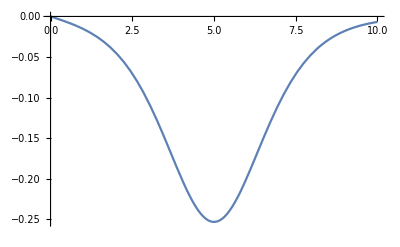

```mathematica
Plot[1/2 Coth[R σ] (-σ Sech[(r-R) σ]^2+σ Sech[(r+R) σ]^2)/.σ->0.5/.R->5,{r,0,10}]
```

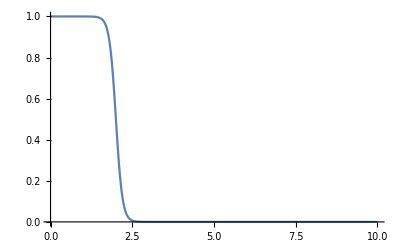

```mathematica
Plot[(Tanh[σ(r+R)]-Tanh[σ(r-R)])/(2Tanh[σ(R)])/.σ->5/.R->2,{r,0,10}]
```

```mathematica
Manipulate[Plot3D[(1/2 Coth[R σ] (-Tanh[(-R+√(z^2+ρ^2)) σ]+Tanh[(R+√(z^2+ρ^2)) σ])),{ρ,-10,10},{z,-10,10}],{σ,0,1},{R,0,10}]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
r=√(ρ^2+z^2)
```

√(z^2+ρ^2)

```mathematica
Manipulate[Plot3D[z/(√(z^2+ρ^2))(1/2 Coth[R σ] (-Tanh[(-R+√(z^2+ρ^2)) σ]+Tanh[(R+√(z^2+ρ^2)) σ])),{ρ,-10,10},{z,-10,10}],{σ,0,1},{R,0,5}]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
weqn=2*D[r^2(D[f[r],{r}]),r]==0;

DSolve[{weqn,{f[∞]==0,f[0]==1}}, f[r], {r}]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

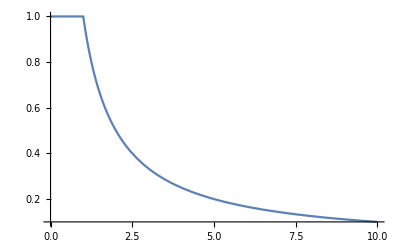

```mathematica
Plot[Min[r0/r,1]/.r0->1,{r,0,10}]
```

```mathematica
Manipulate[Plot3D[z/(√(z^2+ρ^2))(1/2 Coth[R σ] (-Tanh[(-R+√(z^2+ρ^2)) σ]+Tanh[(R+√(z^2+ρ^2)) σ])),{ρ,-10,10},{z,-10,10}],{σ,0,1},{R,0,5}]
```

```mathematica
1/2 Coth[R σ] (-σ Sech[(r-R) σ]^2+σ Sech[(r+R) σ]^2)/.r->√(x^2+z^2)
```

```mathematica
DensityPlot[1/2 Coth[R σ] (-σ Sech[(-R+√(x^2+z^2)) σ]^2+σ Sech[(R+√(x^2+z^2)) σ]^2)/.σ->0.5/.R->5,{{z,0,10},{x,0,10}}]
```

DensityPlot::argrx: DensityPlot called with 2 arguments; 3 arguments are expected.

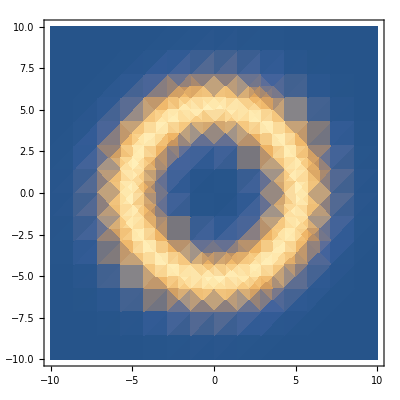

```mathematica
DensityPlot[(√(x^2+z^2))/2 (Coth[R σ] (-σ Sech[(-R+√(x^2+z^2)) σ]^2+σ Sech[(R+√(x^2+z^2)) σ]^2))^2/.σ->0.5/.R->5,{z,-10,10},{x,-10,10}]
```

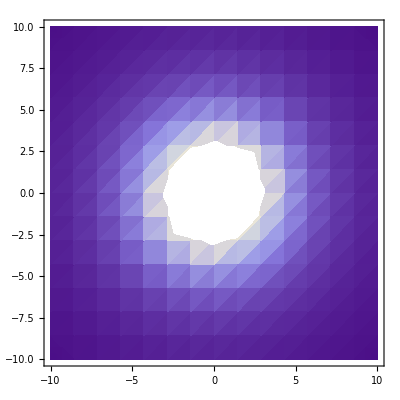

```mathematica
DensityPlot[1/2(Min[1,r0/(x^2+z^2)])/.r0->1,{z,-10,10},{x,-10,10},PlotTheme->"Classic"]
```

```mathematica
D[(Min[r0/r,1]),r]
```

Piecewise[{{0, r0/r≥1}, {-r0/r^2, True}}]

```mathematica
Manipulate[Plot3D[z/(√(z^2+ρ^2))(Min[1,1/(√(ρ^2+z^2))]),{ρ,-10,10},{z,-10,10}, PlotRange->{-1,1}],{σ,0,1},{R,0,5}]
```

```mathematica
NIntegrate[r^2*(1/2 Coth[R σ] (-σ Sech[(r-R) σ]^2+σ Sech[(r+R) σ]^2))^2/.σ->1.9/.R->1,{r,1,∞}]
```

0.537664

```mathematica
NIntegrate[r^2*(D[(Min[r0/r,1]),r])^2/.r0->1,{r,1,∞}]
```

1.

```mathematica
Plot[Min[r0/r,1]/.r0->1,{r,0,10}]
```

-Graphics-